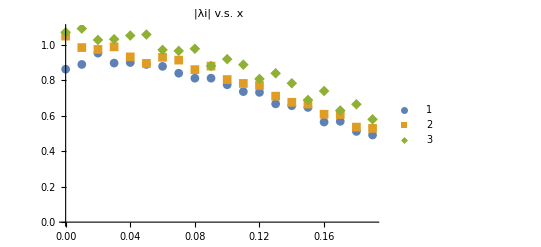

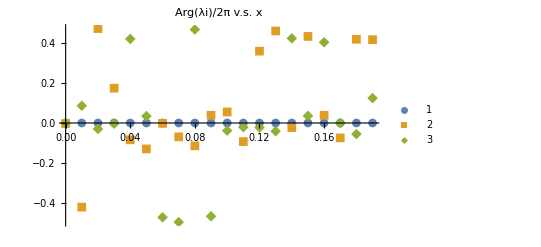

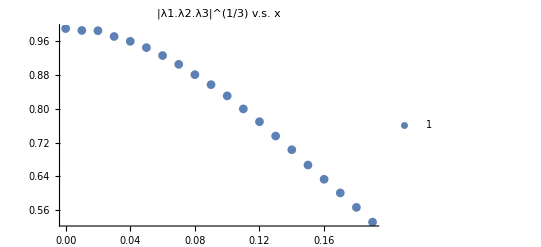

```mathematica
codbar=Import["Google Drive/jie_programs/QHlattice/data_twolaughlin_diaged/twoholelaughlin_may20","Table"];
n:=Length[codbar]
d=Table[codbar[[i]][[1]],{i,1,n,1}];
amp1=Table[{d[[i]],codbar[[i]][[3]]},{i,1,n,1}];
amp2=Table[{d[[i]],codbar[[i]][[5]]},{i,1,n,1}];
amp3=Table[{d[[i]],codbar[[i]][[7]]},{i,1,n,1}];
ang1=Table[{d[[i]],codbar[[i]][[2]]/(2π)},{i,1,n,1}];
ang2=Table[{d[[i]],codbar[[i]][[4]]/(2π)},{i,1,n,1}];
ang3=Table[{d[[i]],codbar[[i]][[6]]/(2π)},{i,1,n,1}];

ListPlot[{amp1,amp2,amp3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λi| v.s. x"]
ListPlot[{ang1,ang2,ang3},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel-> "Arg(λi)/2π v.s. x"]
ListPlot[{(amp1*amp2*amp3)^(1/3)},PlotLegends->{"1","2","3"},PlotMarkers->Automatic, PlotLabel->"|λ1.λ2.λ3|^(1/3) v.s. x"]
```